```mathematica
Clear[LatticeIrrational,latticeRational]
```

```mathematica
LatticeIrrational=Table[{j,0},{j,1,316/2}];
```

```mathematica
latticeRational=Table[{j,0},{j,1,282/2}];
```

```mathematica
largestXRational = 282/2;
largestXIrrational = 316/2;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataLDoSPBC,colorfunc,colorfuncBW]
```

```mathematica
dataLDoSPBC=Import["LDOSParent60DislocationIrrational12to14mM100PBC.dat"];
```

```mathematica
dataLDoSPBC;
```

```mathematica
dataLDoSPBCSorted = SortBy[Last][dataLDoSPBC]
```

{{1,0,1.51973×10^-9},{4,0,2.37922×10^-8},{2,0,3.21313×10^-8},{3,0,5.35861×10^-8},{5,0,1.31977×10^-7},{6,0,5.13479×10^-7},{12,0,5.46476×10^-7},{9,0,6.66825×10^-7},{11,0,1.24669×10^-6},{8,0,1.2574×10^-6},{13,0,1.31587×10^-6},{7,0,1.47044×10^-6},{10,0,1.56083×10^-6},{25,0,2.326×10^-6},{16,0,3.18205×10^-6},{22,0,3.36323×10^-6},{17,0,4.11916×10^-6},{26,0,4.33206×10^-6},{14,0,4.66105×10^-6},{19,0,6.05719×10^-6},{15,0,6.11786×10^-6},{158,0,6.45248×10^-6},{21,0,6.76611×10^-6},{33,0,6.85664×10^-6},{18,0,7.05732×10^-6},{67,0,7.39893×10^-6},{60,0,7.49536×10^-6},{24,0,7.89667×10^-6},{23,0,8.58501×10^-6},{20,0,9.07281×10^-6},{34,0,9.55298×10^-6},{59,0,0.0000106458},{27,0,0.000011867},{63,0,0.0000127337},{66,0,0.0000129368},{30,0,0.0000135474},{46,0,0.0000150111},{68,0,0.0000152129},{47,0,0.000015235},{32,0,0.0000159162},{156,0,0.000016767},{29,0,0.0000170901},{37,0,0.0000180498},{61,0,0.0000184866},{64,0,0.0000186986},{56,0,0.0000201538},{28,0,0.0000229917},{31,0,0.0000234166},{62,0,0.0000247269},{43,0,0.0000252857},{65,0,0.0000253481},{50,0,0.0000255885},{38,0,0.0000291122},{55,0,0.0000319055},{35,0,0.0000333821},{58,0,0.0000364774},{157,0,0.0000400645},{36,0,0.0000402981},{42,0,0.0000408193},{51,0,0.0000417351},{40,0,0.0000431029},{57,0,0.0000445487},{45,0,0.0000447909},{53,0,0.0000459085},{48,0,0.0000460906},{39,0,0.0000476514},{54,0,0.0000521751},{44,0,0.0000552311},{69,0,0.0000553051},{49,0,0.0000564932},{41,0,0.000061455},{52,0,0.0000634238},{155,0,0.000091974},{72,0,0.000165468},{70,0,0.000202286},{154,0,0.000508083},{71,0,0.000551785},{148,0,0.000612818},{151,0,0.000669634},{87,0,0.000758938},{73,0,0.000880519},{84,0,0.00103771},{149,0,0.00122673},{152,0,0.00126581},{147,0,0.00138418},{153,0,0.00147248},{150,0,0.0015631},{86,0,0.00160569},{88,0,0.0016357},{83,0,0.00188341},{85,0,0.00220146},{81,0,0.00233772},{135,0,0.00282431},{144,0,0.00282782},{122,0,0.00286118},{82,0,0.00290122},{113,0,0.00302345},{121,0,0.00306698},{114,0,0.00312381},{100,0,0.00315192},{91,0,0.00329063},{134,0,0.00339824},{101,0,0.0037077},{143,0,0.00422059},{138,0,0.00444416},{146,0,0.00493389},{92,0,0.00493571},{97,0,0.00499219},{125,0,0.00500725},{110,0,0.00533636},{76,0,0.00552149},{74,0,0.00574855},{89,0,0.00575267},{145,0,0.00612933},{131,0,0.00627288},{80,0,0.00640614},{104,0,0.00677043},{90,0,0.00713494},{141,0,0.00727358},{142,0,0.00736645},{139,0,0.0075472},{120,0,0.00766479},{115,0,0.0077557},{136,0,0.00822794},{94,0,0.00830077},{96,0,0.00844982},{117,0,0.00852516},{93,0,0.00855125},{118,0,0.00860472},{126,0,0.00872594},{109,0,0.00922759},{99,0,0.00923163},{130,0,0.00954252},{123,0,0.00994326},{137,0,0.0100288},{105,0,0.0103672},{112,0,0.0105157},{133,0,0.0105452},{140,0,0.010998},{128,0,0.0110355},{98,0,0.0112533},{102,0,0.0114466},{124,0,0.0116111},{107,0,0.0118687},{111,0,0.0123229},{95,0,0.0123781},{119,0,0.0128498},{116,0,0.0128593},{132,0,0.0131891},{127,0,0.0133646},{108,0,0.0142306},{103,0,0.0142929},{129,0,0.0148705},{106,0,0.0160939},{79,0,0.0876721},{77,0,0.0877147},{75,0,0.096434},{78,0,0.20587}}

```mathematica
CutoffData = Select[dataLDoSPBCSorted,#[[3]]>0.007&];
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
colorfuncBW=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]]
```

Function[{v,vmax},Hue[0.5+(0.5 v)/vmax,0,1.-(1. v)/vmax,v/vmax]]

```mathematica
rngOld={0,Max[#]}&@dataLDoSPBC[[All,3]]
```

{0,0.20587}

```mathematica
rng={0,0.22}
```

{0,0.22}

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"1.1"},{rng[[2]]-10^-3,"2.2"}}]
```

```mathematica
(** Crop appropriately and put the numbers in inkscape **)
```

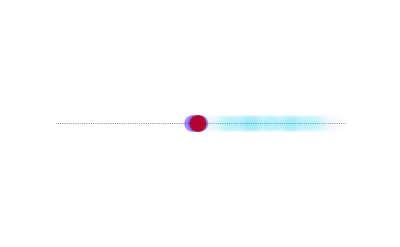

```mathematica
Show[
ListPlot[LatticeIrrational,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {{-10,Max[Flatten[LatticeIrrational]]+10},{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]
}&/@dataLDoSPBCSorted,
BaseStyle-> 18
]

]
```

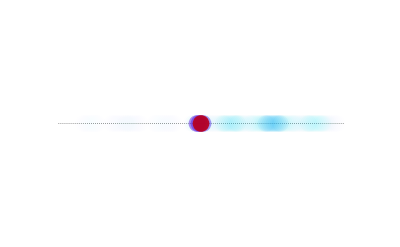

-Graphics-

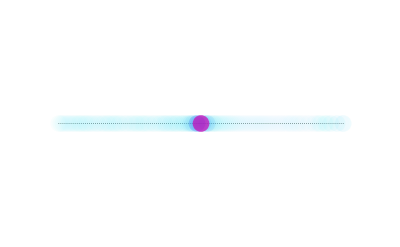

-Graphics-

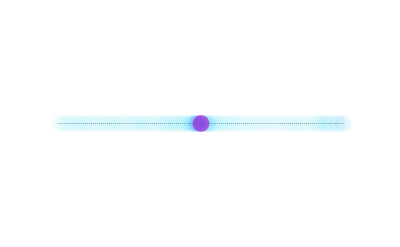

-Graphics-